```mathematica
(*For the following block of code,all you really need to know are what the following 2 functions do.-"Use[n]" is 1 if n is not divisible by the first WheelEntries primes,0 otherwise-"Coprimes[n]" is the sum of Use[1] through Use[n]*)
Clear[d]
WheelEntries=4;
FirstNonWheel =11;
WheelSize:=Product[Prime[j],{j,1,WheelEntries}];
CoprimeCache:=CoprimeCache=Table[CoprimeQ[WheelSize,n],{n,1,WheelSize}]
Use[n_]:=Use[n]=If[CoprimeCache[[Mod[n-1,WheelSize]+1]]==True,1,0]
LegendrePhi[x_,a_]:=LegendrePhi[x,a]=LegendrePhi[x,a-1]-LegendrePhi[x/Prime[a],a-1]
LegendrePhi[x_,0]:=Floor[x]
LegPhiCache:=LegPhiCache=Table[LegendrePhi[n,WheelEntries],{n,1,WheelSize}]
FullWheel:=LegendrePhi[WheelSize,WheelEntries];
Coprimes[n_]:=LegPhiCache[[Mod[n-1,WheelSize]+1]]+Floor[(n-1)/WheelSize] FullWheel

(*There are only 3 changes from the previous version of this code-the use of "Coprimes" in d[n,1,a]-the use of "Use" in d[n,k,a]-the addition of "WheelEntries" in CountPrimes.*)
d[n_,0,a_]:=1
d[n_,1,a_]:=d[n,1,a]=Coprimes[n]-Coprimes[a]
d[n_,k_,a_]:=d[n,k,a]=Sum[If[Use[m]==0,0,Binomial[k,j] d[Floor[n/(m^(k-j))],j,m]],{m,a+1,n^(1/k)},{j,0,k-1}]
RiemannPrimeCounting[n_]:=Sum[(-1)^(k+1)/k d[Floor[n],k,FirstNonWheel-1],{k,1,Log[FirstNonWheel,n]}]
CountPrimes[n_]:=WheelEntries+Sum[MoebiusMu[k] RiemannPrimeCounting[n^(1/k)]/k,{k,1,Log[2,n]}]
```

```mathematica
Timing[CountPrimes[10^10]]
```

{55.459,417828337}

```mathematica
Sum[If[ CoprimeCache[[j]]==True,1,0],{j,WheelSize}]
```

480

```mathematica
WheelSize
```

2310

```mathematica
(* What I want here is a map from index space to wheel space.

so, 1->17
   2->19

 *)
```

```mathematica
CoprimeCache
```

{True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False}

```mathematica
x:=1
```

```mathematica
x2:=Prepend[{1,2,3},x2]
```

```mathematica
Position[{2,4,6,8,10},_?(#>7&)]
```

{{4},{5}}

```mathematica
CoprimeOffsets:=Flatten[Position[CoprimeCache,_?(#==True&)]]
```

```mathematica
CoprimeOffsets
```

{1,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,121,127,131,137,139,143,149,151,157,163,167,169,173,179,181,187,191,193,197,199,209}

```mathematica
FullWheel
```

48

```mathematica
WheelSize
```

210

```mathematica
doid[n_]:=CoprimeOffsets[[Mod[n-1,FullWheel]+1]]+Floor[(n-1)/FullWheel]WheelSize
```

```mathematica
doid[50]
```

221

```mathematica
Clear[ CoprimeOffsets, CoprimeCache, WheelForID]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
WheelEntries=6;
WheelSize:=Product[Prime[j],{j,1,WheelEntries}];
CoprimeCache:=CoprimeCache=Table[If[CoprimeQ[WheelSize,n],1,0],{n,1,WheelSize}]
LegendrePhi[x_,a_]:=LegendrePhi[x,a]=LegendrePhi[x,a-1]-LegendrePhi[x/Prime[a],a-1]
LegendrePhi[x_,0]:=Floor[x]
LegPhiCache3:=LegPhiCache3=Accumulate[CoprimeCache]
FullWheel:=LegendrePhi[WheelSize,WheelEntries];
Coprimes[n_]:=LegPhiCache3[[Mod[n-1,WheelSize]+1]]+Floor[(n-1)/WheelSize] FullWheel
CoprimeOffsets:=CoprimeOffsets=Flatten[Position[CoprimeCache,_?(#==1&)]]
WheelForID[n_]:=WheelForID[n]=CoprimeOffsets[[Mod[n-1,FullWheel]+1]]+Floor[(n-1)/FullWheel]WheelSize
FirstNonWheel :=WheelForID[2]

Clear[DB]
DB[n_,0,a_]:=1
DB[n_,1,a_]:=DB[n,1,a]=Coprimes[n]-Coprimes[WheelForID[a]]
DB[n_,k_,a_]:=DB[n,k,a]=Sum[bin[k,j] DB[Floor[n/(WheelForID[m]^(k-j))],j,m],{m,a+1,Coprimes[Floor[n^(1/k)]]},{j,0,k-1}]
DBz[n_,z_]:=Expand[Sum[bin[z,k] DB[Floor[n],k,1],{k,0,Log[FirstNonWheel,n]}]]
RiemannPrimeCounting[n_]:=Sum[(-1)^(k+1)/k DB[Floor[n],k,1],{k,1,Log[FirstNonWheel,n]}]
CountPrimes[n_]:=WheelEntries+Sum[MoebiusMu[k] RiemannPrimeCounting[n^(1/k)]/k,{k,1,Log[2,n]}]
DBzeros[n_]:=List@@NRoots[DBz[n,z]==0,z][[All,2]]
DBzAlt[n_, z_] := Expand[Product[ 1-z/rho,{rho,DBzeros[n]}]]

AbsoluteTiming[DBz[1000000000,z]]
```

{3.532202,1+(20328191839 z)/420+(29384294573 z^2)/360+(3096475919 z^3)/72+(1028280641 z^4)/144+(253213241 z^5)/720+(1961089 z^6)/720+(199 z^7)/1008}

```mathematica
1+(345725687 z)/60+(410984831 z^2)/45+(61241237 z^3)/16+(64556533 z^4)/144+(2360137 z^5)/240+(5399 z^6)/720
```

```mathematica
DBzeros[100000000]
```

{-1264.47,-36.6817,-6.88326,-2.39112,-1.00658,-1.73548×10^-7}

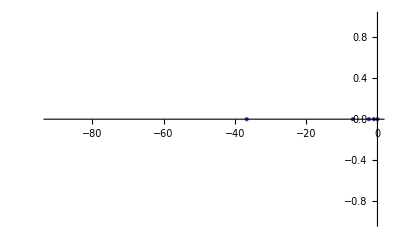

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,DBzeros[100000000]}]]
```

```mathematica
DBz[1000,z]
```

1+(329 z)/2+(49 z^2)/2

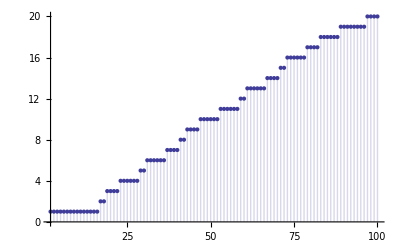

```mathematica
DiscretePlot[DBz[n,1],{n,2,100}]
```

```mathematica
Clear[Dk]
Dk[n_,s_,0] := UnitStep[n-1]
Dk[n_,s_,k_]:=Dk[n,k]=Sum[WheelForID[j]^-s Dk[Floor[n/WheelForID[j]],s,k-1],{j,2,Coprimes[n]}]
Dkz[n_,s_,z_]:=Expand[Sum[bin[z,k] Dk[Floor[n],s,k],{k,0,Log[FirstNonWheel,n]}]]
```

```mathematica
DBz[100000,z]
```

1+(115421 z)/12+(209983 z^2)/24+(9745 z^3)/12+(5 z^4)/24

```mathematica
-N[D[D[Dkz[10000,s,z],z]/.z->0,s]/.s->0] + Sum[ Log[Prime[j]]*Floor[Log[Prime[j],10000]],{j,1,WheelEntries}]
```

10013.4

```mathematica
Sum[ N[MangoldtLambda[j]],{j,2,10000}]
```

10013.4

```mathematica
Prime[1
]
```

2

```mathematica
(D[Dkz[10000,-1,z],z]/.z->0) + Sum[k^-1 Prime[j],{j,1,WheelEntries}, {k,1,Log[Prime[j],10000]}]
```

2080384591267/360360

```mathematica
Sum[ FullSimplify[ j MangoldtLambda[j]/Log[j]],{j,2,10000}]
```

2082395892559/360360

```mathematica
Sum[k^-1,{j,1,WheelEntries}, {k,1,Log[Prime[j],100]}]
```

143/15

```mathematica
D[Dkz[100,0,z],z]/.z->0
```

19

```mathematica
Clear[ CoprimeOffsets, CoprimeCache, WheelForID, Coprimes, WheelSize, LegPhiCache]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
WheelEntries=7;
WheelSize:=WheelSize=Product[Prime[j],{j,1,WheelEntries}];
CoprimeCache:=CoprimeCache=Table[If[CoprimeQ[WheelSize,n],1,0],{n,1,WheelSize}]
LegPhiCache:=LegPhiCache=Accumulate[CoprimeCache]
FullWheel:=FullWheel = LegPhiCache[[WheelSize]]
CoprimeOffsets:=CoprimeOffsets=Flatten[Position[CoprimeCache,_?(#==1&)]]
Coprimes[n_]:=Coprimes[n]=LegPhiCache[[Mod[n-1,WheelSize]+1]]+Floor[(n-1)/WheelSize] FullWheel
WheelForID[n_]:=WheelForID[n]=CoprimeOffsets[[Mod[n-1,FullWheel]+1]]+Floor[(n-1)/FullWheel]WheelSize
FirstNonWheel :=FirstNonWheel=WheelForID[2]
```

```mathematica
Clear[DB]
DB[n_,0,a_]:=1
DB[n_,1,a_]:=DB[n,1,a]=Coprimes[n]-Coprimes[WheelForID[a]]
DB[n_,2,a_]:=DB[n,2,a]=(Coprimes[Floor[n^(1/2)]]-a)+2Sum[ DB[Floor[n/WheelForID[m]],1,m],{m,a+1,Coprimes[Floor[n^(1/2)]]}]
DB[n_,k_,a_]:=DB[n,k,a]=(Coprimes[Floor[n^(1/k)]]-a)+k Sum[ DB[Floor[n/(WheelForID[m]^(k-1))],1,m],{m,a+1,Coprimes[Floor[n^(1/k)]]}]+Sum[bin[k,j] DB[Floor[n/(WheelForID[m]^(k-j))],j,m],{m,a+1,Coprimes[Floor[n^(1/k)]]},{j,2,k-1}]
DBz[n_,z_]:=Expand[Sum[bin[z,k] DB[Floor[n],k,1],{k,0,Log[FirstNonWheel,n]}]]
RiemannPrimeCounting[n_]:=Sum[(-1)^(k+1)/k DB[Floor[n],k,1],{k,1,Log[FirstNonWheel,n]}]
CountPrimes[n_]:=WheelEntries+Sum[MoebiusMu[k] RiemannPrimeCounting[n^(1/k)]/k,{k,1,Log[2,n]}]
DBzeros[n_]:=List@@NRoots[DBz[n,z]==0,z][[All,2]]
DBzAlt[n_, z_] := Expand[Product[ 1-z/rho,{rho,DBzeros[n]}]]
```

```mathematica
AbsoluteTiming[DBz[100000000000,z]]
```

{29.683698,1+(86479442449 z)/21+(7940004689507 z^2)/1008+(1153363494317 z^3)/240+(3301789279217 z^4)/2880+(4925259257 z^5)/48+(783748475 z^6)/288+(9638813 z^7)/840+(20491 z^8)/20160}

```mathematica
1+(345725687 z)/60+(410984831 z^2)/45+(61241237 z^3)/16+(64556533 z^4)/144+(2360137 z^5)/240+(5399 z^6)/720
```

```mathematica
AbsoluteTiming[DBzAlt[100000000000, 1]]
```

{0.002,1.80525×10^10}

```mathematica
DBzeros[100000000000]
```

{-11047.9,-197.953,-28.2135,-8.55061,-3.75578,-2.04436,-1.00016,-2.42832×10^-10}

```mathematica
CountPrimes[100000000000]
```

4118054813

```mathematica
AbsoluteTiming[PrimePi[100000000000]]
```

{0.4420253,4118054813}

```mathematica
WheelSize
```

510510

```mathematica
10^11
```

100000000000